```mathematica
g[om_] = Sqrt[Pi/om] Piecewise[{{LegendreP[-1/2,0,3, (om^2+1)/(2om)] + 3/2 LegendreP[-1/2,-1,3, (om^2+1)/(2om)], om<1},
{LegendreP[-1/2,0,3, (om^2+1)/(2om)] - 3/2 LegendreP[-1/2,-1,3, (om^2+1)/(2om)], om≥1}}]
```

√(1/om) √π (Piecewise[{{(2 EllipticK[1/2 (1-(1+om^2)/(2 om))])/π+3/2 LegendreP[-1/2,-1,3,(1+om^2)/(2 om)], om<1}, {(2 EllipticK[1/2 (1-(1+om^2)/(2 om))])/π-3/2 LegendreP[-1/2,-1,3,(1+om^2)/(2 om)], om≥1}, {0, True}}])

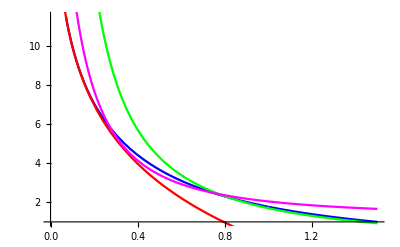

```mathematica
p1=Plot[g[x],{x,0.0000001,1.5}, PlotStyle->Blue];
p2=Plot[-4.336 Log[x],{x,0.0000001,1.5}, PlotStyle->Red];
p3=Plot[2/x^1.2-0.3,{x,0.0000001,1.5}, PlotStyle->Green];
p4=Plot[1/(x+0.11)^1.6 + 1.2,{x,0.0000001,1.5}, PlotStyle->Magenta];
Show[p1,p2,p3,p4]
```

```mathematica
2
```

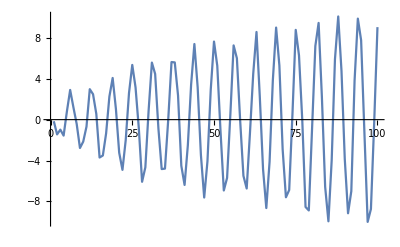

```mathematica
Table[Sqrt[x] Cos[x]+RandomReal[{-1,1}],{x,100}];
ListLinePlot[%]
```

```mathematica
FindFit[%%,a x^b Cos[c x],{a,b,c},x]
```

{a→5.09064,b→0.231126,c→1.00014}

{a→-0.00191587,b→-0.4505,c→1.00111,d→2.18345}→a

√π

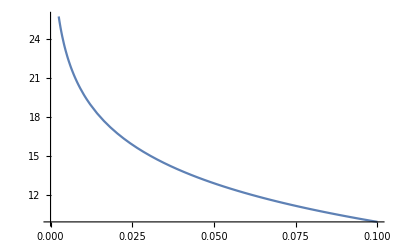

```mathematica
√π
Plot[-4.3Log[x],{x,000000,0.1}]
```